# Braitenberg’s Type 1 vehicles analysis

This notebook contains definition and graphs for the dynamic differential  equations governing the motion of a Type 1 Braitenberg vehicle (both a and b variants), endowed with a single sensor either omni-directional or pointing forward and with a field of view of 180 degrees.

## Systems with Omndirectional sensors

For a Type 1a system with a omndirectional sensor and the input decaying according the inverse square law, we have the following equation for the system as a whole:

```mathematica
braiten1aOmni(x_):=(a K S)/((s-x)^2+1)
```

whose phase portrait is as follows:

```mathematica
Manipulate[Plot[(α*K*S)/(1+(s-x)^n),{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,ẋ}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{α,1,"alpha: Sensor efficiency"},0,1,Appearance->"Labeled"},{{K,1,"K: Input to Output Factor"},0,1,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

Instead for a Type 1b system with a omnidirectional sensor, our equation becomes:

```mathematica
braiten1bOmni(x_):=(K ((s-x)^2+1))/(α S)
```

whose phase portrait is as follows:

```mathematica
Manipulate[Plot[(K*((s-x)^n))/(α*S),{x,-10,20},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,ẋ}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{α,1,"alpha: Sensor efficiency"},0,1,Appearance->"Labeled"},{{K,1,"K: Input to Output Factor"},0,1,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

## Systems with directional sensors

```mathematica
braiten1aDot(x_):=(α K S)/(ⅇ^(β (s-x))+(s-x)^2+1)
```

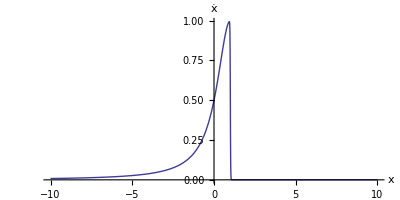

```mathematica
Plot[braiten1aDot[x],{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel-> {x,OverDot[x]}]
```

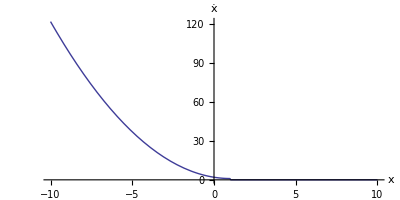

```mathematica
Plot[braiten1bDot[x],{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel-> {x,OverDot[x]}]
```

```mathematica
braiten1bDot(x_):=(K ((s-x)^2+1))/((α S) (ⅇ^(β (s-x))+1))
```

```mathematica
braiten1aDot(x_):=(α K S)/(ⅇ^(β (s-x))+(s-x)^2+1)
```

```mathematica
Manipulate[Plot[(K ((s-x)^2+1))/((α S) (ⅇ^(β (s-x))+1)),{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,ẋ}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{α,1,"alpha: Sensor efficiency"},0,1,Appearance->"Labeled"},{{β,-10,"Beta: Logistic parameter"},-20,0,Appearance->"Labeled"},{{K,1,"K: Input to Output Factor"},0,1,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

```mathematica
Manipulate[Plot[(α K S)/((s-x)^n+ⅇ^(β (s-x))+1),{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,ẋ}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{α,1,"alpha: Sensor efficiency"},0,1,Appearance->"Labeled"},{{β,-10,"Beta: Logistic parameter"},-20,0,Appearance->"Labeled"},{{K,1,"K: Input to Output Factor"},0,1,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

Multi-sensor analysis
First, let us now rewrite the previous functions in terms of sensor readings (y  functions), actuator functions (u functions) and let’s Mathematica do the composition to obtain the  dx/dt  function to be plotted for qualitative analysis).
First the sensor function, rewritten with all parameters as arguments. Notice that this is a generic function that can then be reused, once parameters are properly set, for different sensors:

```mathematica
sensorGenericForward[x_,s_,α_,S_,n_,β_] := (α S)/((ⅇ^(β (s-x))+1) ((Abs [s-x])^n+1))
```

Now let’s test it with a manipulated chart  (logistic coefficient β is fixed at -10):

```mathematica
Manipulate[Plot[sensorGenericForward[x,s,α,S,n,-10],{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,stimulus}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{α,1,"alpha: Sensor efficiency"},0,1,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

We could then define specific forward sensors for different stimulus sources.Notice, however, that the previous sensor definition mixes up world-related parameters (S, s, and n, which define the physical features of the stimulus source), with robot-related paramters (α, the sensor’s efficiency) and math parameters (β, the logistic function coefficient). It would be better to separate those parameters in lists. However, keeping things simple and proceeding with  the sensor function just defined for now.
In a 1-sensor situation, the actuator command function u, would then simply multiply (or divide)  the output of  s specific sensor for a constant, or apply other more sophisticated manipulations. To replicate the previous exercise, we could have the following actuator function for a Type 1a vehicle:

```mathematica
u1a[x_,s_,S_,n_]:= 1/sensorGenericForward[x,s,1,S,n,-10] 
Plot[u1a[x,0,1,1],{x,-10,10},PlotRange->Full]
```

-Graphics-

The state dynamics function dx/dt  is just identical to u in our simple case (no dynamics), so we could just write:

```mathematica
xDot := u1a[x_,s_,S_,n_]
```

And now we can test with our manipulated chart, obtaining a result analogous to the previous one:

```mathematica
Manipulate[Plot[xDot[x,s,S,n],{x,-10,10},PlotRange->Full,AspectRatio->.5,AxesLabel->{x,ẋ}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{S,1,"S: Source strength"},1,10,Appearance->"Labeled"},{{n,2,"n: Stimulus degradation"},1,3,Appearance->"Labeled"},ControlPlacement->Left]
```

## System with Homeo unit controlling sensor

[The following analysis is actually wrong. I confused/conflated x as the output of the Homeo unit, with x as  the displacement of the vehicle. The two are related, but not identical. The output of the Homeo unit is actually the input to the motor, hence (dynamics aside) the velocity (not the displacement) of the unit. Hence, we should replace the term denoting the input to the unit with a function of t  expressed via the velocity of the vehicle].

```mathematica
Manipulate[Plot[1/m*(-w*x+1/(1+(s-x)^2)),{x,-10,10},PlotRange->All,AspectRatio-> 1,AxesLabel->{x,y}],{{s,0,"s: Stimulus location"},-50,50,Appearance->"Labeled"},{{w,1,"w: weight"},0.01,1,Appearance->"Labeled"},{{m,2,"m: mass"},0.001,1003,Appearance->"Labeled"},ControlPlacement->Left]
```

```mathematica
Solve[{y==0,1/m*(-w*x+1/(1+(s-x)^2))==0},{x,y}]
```

{{x→(2 s)/3-(2^(1/3) (3 w^2-s^2 w^2))/(3 w (27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))+((27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))/(3 2^(1/3) w),y→0},{x→(2 s)/3+((1+ⅈ √3) (3 w^2-s^2 w^2))/(3 2^(2/3) w (27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))-((1-ⅈ √3) (27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))/(6 2^(1/3) w),y→0},{x→(2 s)/3+((1-ⅈ √3) (3 w^2-s^2 w^2))/(3 2^(2/3) w (27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))-((1+ⅈ √3) (27 w^2-18 s w^3-2 s^3 w^3+3 √3 √(27 w^4-36 s w^5-4 s^3 w^5+4 w^6+8 s^2 w^6+4 s^4 w^6))^(1/3))/(6 2^(1/3) w),y→0}}

```mathematica
Manipulate[Plot[1/(v*(1+(s-x)^2))-(w*x)/v,
				{x,-10,10},
				PlotRange->Automatic,
				AspectRatio-> 1,
				AxesLabel->{x,y}],
		{{s,5,"s: Stimulus location"},-50,50,Appearance->"Labeled"},
		{{w,0.11,"w: weight"},0.01,1,Appearance->"Labeled"},
		{{v, 10,"viscosity"},1,100,Appearance ->"Labeled"},
		{{m,10,"m: mass"},0.001,1003,Appearance->"Labeled"},
		ControlPlacement->Left]
```

```mathematica
Simplify[1/(20*(1+(5-x)^2))-(0.1*x)/20]
```

1/(20 (1+(-5+x)^2))-0.005 x

```mathematica
Reduce[%>0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x<0.46337||3.69323<x<5.8434

```mathematica
<<EquationTrekker`
```

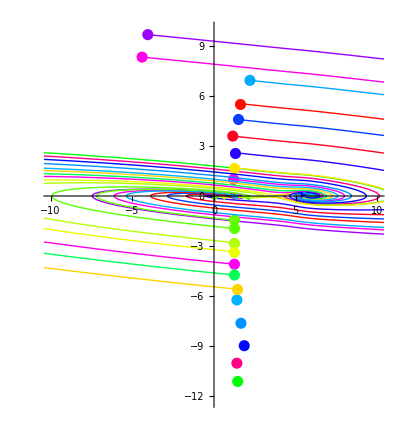
{EquationTrekkerState["Notebook$$110$310169`x''Notebook$$110$310169`xt0100","{m → 10., s → 5., v → 1., w → 0.1}",TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>]
TrekData["0.Notebook$$110$310169`x'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[x''[t]==1/m*(-v*x'[t]-w*x[t]+1/(1+(s-x[t])^2)),x,{t,0,100},TrekParameters->{v->{1,{1,20}},  
w->{0.1,{0.001,1}},
s->{5,{0,20}},
m-> {10,{1,1000}}},
PlotRange->{{-10,10},{-10,10}}]
```